# End - of - Semester Project : Chernoff Faces

### Karan Vikyath Veeranna Rupashree (veerannarupa@wisc.edu) Anmol Sharma (sharma265@wisc.edu)

### Chernoff Faces

A Chernoff face is a simple sketch of a human face that is parameterized by a few variables. By manipulating the variables, it is possible to achieve a wide range of expressions. Here are a few auxiliary functions (evaluate these before running the Manipulate) below.

```mathematica
face=Circle[{0,0},{1,1.2}];pupNow={0,0};left=1;right=2;
eyeRadius=0.18;eyeCenter={{-0.4,0.15},{0.4,0.15}};pupilRadius=0.09;
browUp=0.25;browW=0.2;browAng=Pi/20;
eye[side_,eccen_]:={Black,Circle[eyeCenter[[side]],{eyeRadius+0.05,eyeRadius+eccen}]};
pupil[side_,pup_,eccen_]:={Disk[eyeCenter[[side]]+pup+{0,pup[[2]] eccen},pupilRadius+Max[0,eccen/3]],Black,Disk[eyeCenter[[side]]+pup+{0,pup[[2]] eccen},0.03]};
browDraw[side_,{browAng_,browLift_},eccen_]:=Rotate[{Thickness[0.01],Line[{{eyeCenter[[side]]+{-browW,browLift+browUp+0.5 eccen},eyeCenter[[side]]+{browW,browLift+browUp+0.5 eccen}}}]},2 (side-1.5) browAng];
mouthDraw[s_]:=ParametricPlot[{Cos[u],-s Sin[u]},{u,Pi/6,Pi-Pi/6},Axes->False,PlotStyle->{Red,Thickness[0.02]},PlotRange->All];
```

Now you can create many expressive faces by moving the sliders and grabbing the eyes with the mouse. See if you can make it happy. Sad? Angry?

```mathematica
Manipulate[eyeMat={{1/(eyeRadius-pupilRadius/2),0},{0,1/(0.15+eyes-pupilRadius/2)}};
If[Norm[eyeMat.(pup-eyeCenter[[left]])]<1,pupNow=pup-eyeCenter[[left]];];
If[Norm[eyeMat.(pup-eyeCenter[[right]])]<1,pupNow=pup-eyeCenter[[right]];];
Graphics[{face,eye[left,eyes],eye[right,eyes],Blue,pupil[left,pupNow,eyes],pupil[right,pupNow,eyes],Black,browDraw[left,brows,eyes],browDraw[right,brows,eyes],Inset[mouthDraw[mouth],{0,-0.5}]},ImageSize->{400,450}],{{brows,{-Pi/20,0}},{-0.6,0},{0.6,0.15},ControlPlacement->Left},{{eyes,0},-0.07,0.07,ControlPlacement->Left,ControlType->VerticalSlider},{{mouth,0.15},-0.401,0.4,0.01,ControlPlacement->Left,ControlType->VerticalSlider},{{pup,{0,0}},Locator,Appearance->None},SaveDefinitions->True]
```

I originally wrote this in answer to a StackExchange question:

```mathematica
URL["https://mathematica.stackexchange.com/questions/143988/how-to-define-a-function-to-produce-a-chernoff-face"]
```

URL[https://mathematica.stackexchange.com/questions/143988/how-to-define-a-function-to-produce-a-chernoff-face]

### Chernoff Photos #1

Your goal in this part of the project is to start with a full-face photo, and to create a Manipulate that will cause the photo to undergo expression changes analogous to the simple line drawing above. So if your friend in the photo is smiling, you can grab the mouth slider and make them sad. If their eyebrows are curved gently down, you can make them angry by moving the brows slider. If the eyes are narrow, you can widen them with the eye slider to make them look surprised.

In order to accomplish this task, you will need to locate facial features. Fortunately, there is a command called

```mathematica
?FacialFeatures
```

that does a pretty reasonable job. You will want to study the help file for this function. The parent function FeatureExtract may also be useful (though it may not be needed, depending on how you proceed). Of course, you will also want to use some of the spatial mapping functions like those in the Spatial Mappings section of the Visual Vocabulary.

Start with some of the photos from actors and characters from Game of Thrones. Then do the same kind of thing for (at east) 3 other photo images of faces. Perhaps a self-portrait would be fitting.

For this project, you should pass in your function (a Manipulate somewhat similar to the above) along with several examples of how it works on photos of different faces. Show that you can make the faces change expressions. Good luck and have fun!

```mathematica
gamePeople=-Graphics-;
faceJon = -Graphics-;
```

```mathematica
addCorners[feat_,{width_,height_}]:=Block[{feattmp=feat,xcenter,ycenter,xmin,xmax,ymin,ymax},xcenter=feat["OutlinePoints"][[{1,-1},1]]//Mean;
ycenter=feat["NosePoints"][[1,2]];
xmin=xcenter-width/2;
xmax=xcenter+width/2;
ymin=ycenter-height/2;
ymax=ycenter+height/2;
feattmp["Corners"]={{xmin,ymin},{xmin,ymax},{xmax,ymax},{xmax,ymin}};
feattmp]

eyePoints[pointsEyes_, size_]:=
Module[{updatedPoints = {}},
yEyes = Last/@pointsEyes;
xEyes = First/@pointsEyes;
medianX = Median[xEyes];
centralDistances = Abs[xEyes-medianX];
centralDistances  = Abs[centralDistances-Max[centralDistances]];
movementAlphas = centralDistances/Max[centralDistances];

yEyeBisector = (Max[yEyes]+Min[yEyes])/2;
Do[
If[pointsEyes[[i]][[2]]>yEyeBisector,updatedPoints = Append[updatedPoints, {pointsEyes[[i]][[1]],pointsEyes[[i]][[2]]+ movementAlphas[[i]]*size/2}], updatedPoints = Append[updatedPoints, {pointsEyes[[i]][[1]],pointsEyes[[i]][[2]]- movementAlphas[[i]]*size/2}]],
{i, Length[yEyes]}
];
updatedPoints
]

browPoints[pointsEyeBrows_, angle_, translate_]:=

Module[{updatedPoints = {}},
xEyesB = First/@pointsEyeBrows;
yEyesB = Last/@pointsEyeBrows;

Do[
updatedPoints = Append[updatedPoints, {pointsEyeBrows[[i]][[1]],pointsEyeBrows[[i]][[2]]+ translate}],
{i, Length[yEyesB]}
];
(*rotation*)
centralPoint = {Mean[xEyesB], Mean[yEyesB]};
rotation=RotationTransform[angle, centralPoint];
updatedPoints = rotation[updatedPoints];
updatedPoints
]

mouthPoints[pointsMouth_, size_]:=
(*size: y axis movement*)
Module[{updatedPoints = {}},
xMouth = First/@pointsMouth;
yMouth = Last/@pointsMouth;
medianX = Median[xMouth];
centralDistances = Abs[xMouth-medianX];
movementAlphas = centralDistances/Max[centralDistances];


Do[
updatedPoints = Append[updatedPoints, {pointsMouth[[i]][[1]],pointsMouth[[i]][[2]]+ movementAlphas[[i]]*size}],
{i, Length[yMouth]}
];
updatedPoints
]

(*Extended Feature Generator*)
OrgFeatureExtender[img_, faceFeatures_]:=
Module[{},
xcenter=Mean[faceFeatures["OutlinePoints"][[{1,-1},1]]];
ycenter=faceFeatures["NosePoints"][[1,2]];
{width,height}=Floor[Transpose[2*(ImageDimensions[img]-Transpose[{xcenter,ycenter}])]];
exFeats=addCorners[faceFeatures,{width,height}];
exFeats
]

(*Main expression generator*)
FaceGenerator[img_,faceFeatures_, eyesSize_, mouthShape_, {browAngle_,browsTranslate_}]:=
(*
input variables: image of face, face features, eyesSize: how wide or narrow from current position, mouthShape: Moving edges of lips up or down, brow angle to rotate brow and brow tranlate to move the brow up or down
*)
Module[{},
featsnew = faceFeatures;
featsnew["RightEyePoints"] = eyePoints[faceFeatures["RightEyePoints"], eyesSize];
featsnew["LeftEyePoints"] = eyePoints[faceFeatures["LeftEyePoints"], eyesSize];

featsnew["RightEyebrowPoints"] = browPoints[faceFeatures["RightEyebrowPoints"], -browAngle, browsTranslate];
featsnew["LeftEyebrowPoints"] = browPoints[faceFeatures["LeftEyebrowPoints"], browAngle, browsTranslate];

featsnew["MouthExternalPoints"] = mouthPoints[faceFeatures["MouthExternalPoints"],mouthShape];

orgPoints =Flatten[Values[faceFeatures], 1];
newPoints =Flatten[Values[featsnew], 1];
pMeans=Mean/@Transpose[{orgPoints,newPoints}];
ldp=ListDensityPlot[ArrayPad[pMeans,{0,{0,1}}],Mesh->All,ColorFunction->(White&)];
trianglesOrder=First@Cases[ldp,Polygon[idx_]:>idx,Infinity];

trianglesOrg=orgPoints[[#]]&/@trianglesOrder;
trianglesNew=newPoints[[#]]&/@trianglesOrder;
{width, height} = ImageDimensions[img];
Image[Graphics[{Texture[img],MapIndexed[Polygon[#,VertexTextureCoordinates->({#[[1]]/width,#[[2]]/height}&/@trianglesOrg[[First[#2]]])]&,trianglesNew]}]]
]

FeaturesGenerator[img_]:=
Module[{},
faceFeatures = First@FacialFeatures[img, "Landmarks"];
dropFeatures = KeyDrop[faceFeatures, "MouthInternalPoints"];
finalFeatures = OrgFeatureExtender[img, dropFeatures];
finalFeatures
]
```

```mathematica
faceFeatures1 = FeaturesGenerator[faceJon];
FaceGenerator[faceJon,faceFeatures1, 0, 0, {Pi/100,0}]
```

-Graphics-

```mathematica
(*Implementing with Manipulate:)*)
Manipulate[Quiet@FaceGenerator[faceJon,faceFeatures1, eyes, mouth, brows], {{eyes, 0, "Eyes"}, -20, 20, 0.5,ControlPlacement->Left, ControlType->VerticalSlider}, {{mouth, 0, "Mouth"}, -30,30, 1, ControlPlacement->Left, ControlType->VerticalSlider},
{{brows,{-Pi/9, Pi/9},"Eyebrows"},{-0.25,-20},{0.25,20},ControlPlacement->Left,ContinuousAction->False}]
```

```mathematica
imageTest1= -Graphics-;
imageTest2= -Graphics-;
imageTest3=-Graphics-;
```

```mathematica
faceFeatures2 = FeaturesGenerator[imageTest1];Manipulate[Quiet@FaceGenerator[imageTest1,faceFeatures2, eyes, mouth, brows], {{eyes, 0, "Eyes"}, -20, 20, 0.5,ControlPlacement->Left, ControlType->VerticalSlider}, {{mouth, 0, "Mouth"}, -30,30, 1, ControlPlacement->Left, ControlType->VerticalSlider},
{{brows,{-Pi/9, Pi/9},"Eyebrows"},{-0.25,-20},{0.25,20},ControlPlacement->Left,ContinuousAction->False}]

faceFeatures3= FeaturesGenerator[imageTest2];
Manipulate[Quiet@FaceGenerator[imageTest2,faceFeatures3, eyes, mouth, brows], {{eyes, 0, "Eyes"}, -20, 20, 0.5,ControlPlacement->Left, ControlType->VerticalSlider}, {{mouth, 0, "Mouth"}, -30,30, 1, ControlPlacement->Left, ControlType->VerticalSlider},
{{brows,{-Pi/9, Pi/9},"Eyebrows"},{-0.25,-20},{0.25,20},ControlPlacement->Left,ContinuousAction->False}]

faceFeatures4 = FeaturesGenerator[imageTest3];
Manipulate[Quiet@FaceGenerator[imageTest3,faceFeatures4, eyes, mouth, brows], {{eyes, 0, "Eyes"}, -20, 20, 0.5,ControlPlacement->Left, ControlType->VerticalSlider}, {{mouth, 0, "Mouth"}, -30,30, 1, ControlPlacement->Left, ControlType->VerticalSlider},
{{brows,{-Pi/9, Pi/9},"Eyebrows"},{-0.25,-20},{0.25,20},ControlPlacement->Left,ContinuousAction->False}]
```

### Chernoff Photos #2

In the second part of the project, you are asked to do something interesting with your Chernoff photo-faces method from Part #1. What do I mean by “interesting”? Below are some suggestions, but please feel free to think up your own. Creativity will be rewarded.

Example #1: Mathematica’s function CurrentImage[] gets an image from the computer’s camera. Use the CurrentImage[] as input to the Chernoff photo-face by making the eyes look in whatever direction things are changing the most.

Example #2: Choose a .wav file of a poem and have the Chernoff photo-face “read” the poem with expressions.

Example #3: Choose a .wav file of a song and have the Chernoff photo - face "dance" in response to the music.

Example #4: Pick a data set and have the Chernoff photo-face move in response to the data. The data may be from anywhere: NASA has lots of data from sunspots, think of animating weather-pattern data. There is a large variety of “curated data” available right from within Mathematica:

```mathematica
URL["https://reference.wolfram.com/language/howto/UseCuratedData.html"]
```

URL[https://reference.wolfram.com/language/howto/UseCuratedData.html]

These include AstronomicalData, ChemicalData, CityData, CountryData, ExampleData, ElementData, FinancialData, GraphData, IsotopeData, KnotData, LatticeData, ParticleData, PolyhedronData, WordData. Of course you can pick other data as you wish.

## Financial Data

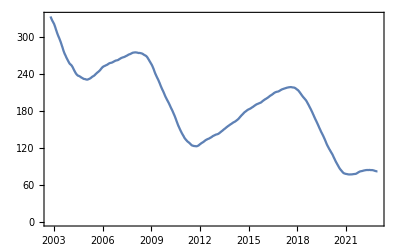

```mathematica
data=TimeSeries@FinancialData["GE","Jan. 1, 2000"];
DateListPlot[MovingAverage[data,700]] (* Moving average for a smoother graph*)
```

#### Moving the facial expressions according to the changes in Financial data. The face gets happier as money increases and gets sadder as money decreases.

```mathematica
valuesFinancial = MovingAverage[data,700]["Values"];
```

```mathematica
brows = 0;
eyes = 0;
mouth = 0; (*Initializing features positions*)
faceFeats = FeaturesGenerator[imageTest1];
img = ConstantArray[0,102];
count=1;
For[i=1,i<=Length@valuesFinancial,i+=50,
If[valuesFinancial[[i]]<valuesFinancial[[i+1]],{brows+=3,eyes+=3,mouth+=3},{brows-=3,eyes-=3,mouth-=3}];
img[[count]] = ImageCollage[{FaceGenerator[imageTest1,faceFeats,mouth, eyes, {Pi/100,brows}],ListPlot[{{i,valuesFinancial[[i]]}},PlotRange->{{0,5000},{0,400}},PlotStyle->{Red,PointSize[0.02]}]}];
count+=1
]
```

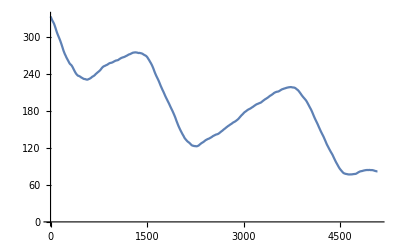

```mathematica
ListLinePlot[valuesFinancial]
SlideShowVideo[img->0.1]
```